## -Graphics-

```mathematica
R= 13.05/2*10^-3;
A=π R^2;
μ0 = 1.26*10^-6;
L = 6.55*10^-3;
```

```mathematica
dataRaw = {
{5.30,0.02},
{4.30, 0.04},
{3.70, 0.09},
{3.20, 0.12},
{2.80, 0.16},
{2.40, 0.27},
{2.2, 0.35},
{2.0, 0.47},
{1.6, 0.73},
{1.8, 0.54},
{1.5, 1.09}
} ; (*s,cm / Force,N*)
```

```mathematica
data = Table[{dataRaw[[i, 1]] * 10^-2, dataRaw[[i, 2]]}, {i, 1, Length@data}]
```

{{0.053,0.02},{0.043,0.04},{0.037,0.09},{0.032,0.12},{0.028,0.16},{0.024,0.27},{0.022,0.35},{0.02,0.47},{0.016,0.73},{0.018,0.54},{0.015,1.09}}

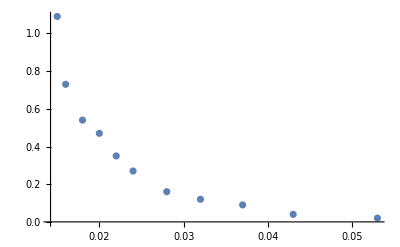

```mathematica
ListPlot[data]
```

```mathematica
dataNormed = Table[{
(1/data[[i, 1]]^2+1/(data[[i,1]] +2L)^2-2/(data[[i,1]] + L)^2),
data[[i, 2]]
},
{i, 1, Length@data}
]
```

{{20.8893,0.02},{43.9779,0.04},{74.3478,0.09},{122.4,0.12},{192.044,0.16},{319.711,0.27},{424.118,0.35},{575.462,0.47},{1154.04,0.73},{801.935,0.54},{1404.28,1.09}}

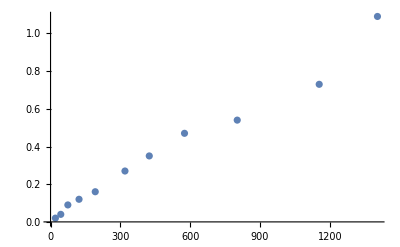

```mathematica
ListPlot[dataNormed]
```

```mathematica
fitLine = Fit[dataNormed, {0,x}, x]
```

0.+0.000728514 x

```mathematica
k = 0.0007285138243203079; (* fitLine = 0 + k x*)
```

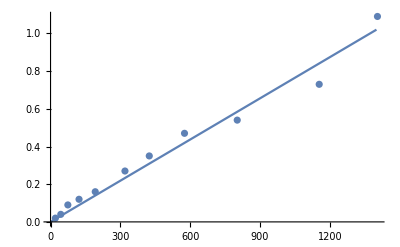

```mathematica
Show[ListPlot[dataNormed], Plot[fitLine,{x, 0, 1400}]]
```

## k = (B0^2 A^2(L^2+R^2))/(π μ0 L^2)

```mathematica
B0 = √((k π μ0 L^2)/(A^2(L^2+R^2))) (* The value we wanted to find!*)
```

0.284434

## The same for 2 magnets:

```mathematica
dataRaw2 = {
{8.8, 0.012},
{8.3, 0.018},
{7.4, 0.024},
{6.5, 0.03},
{5.8, 0.068},
{5.5, 0.074},
{5.1, 0.092},
{4.8, 0.103},
{4.2, 0.142}
(*{3.9, 0.16},
{3.5, 0.216},
{3, 0.303},
{2.5, 0.445},
{2.2, 0.612}*)
}; (* cm,N*)
```

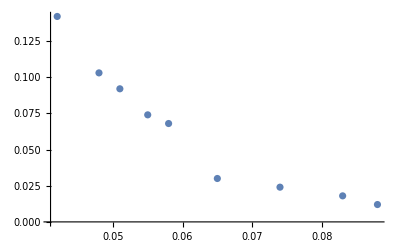

```mathematica
data2 = Table[{dataRaw2[[i, 1]] * 10^-2, dataRaw2[[i, 2]]}, {i, 1, Length@dataRaw2}];
ListPlot[data2]
```

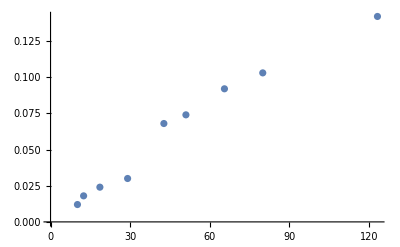

```mathematica
dataNormed2 = Table[{
(1/data2[[i, 1]]^2+1/(data2[[i,1]] +4L)^2-2/(data2[[i,1]] + 2L)^2),
data2[[i, 2]]
},
{i, 1, Length@data2}
];
ListPlot[dataNormed2]
```

```mathematica
fitLine2 = Fit[dataNormed2, {0, x}, x]
```

0.+0.00126411 x

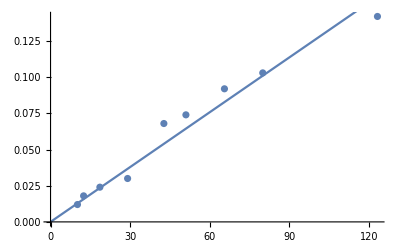

```mathematica
Show[ListPlot[dataNormed2], Plot[fitLine2, {x, 0, 150}]]
```